### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
(*data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];*)
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

793

```mathematica
(*Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];*)
```

### After simulation:

```mathematica
ker
```

{10,16,-5,-13,-10,-2,3,14,-1,4,-3,0}

```mathematica
expected
```

{0,-45,72,-22,184,-26,-64,-26,29,202,159,-134,-478,-42,252,593,5,-4,-183,-243,147,143,217,-225,89,131,233,75,201,-492,-339,129,150,319,390,21,-59,137,-189,-45,-47,206,145,289,-359,82,-218,130,141,423,24,-133,-594,-104,94,471,141,-76,-150,41,-225,-556,-281,605,760,-80,-478,-793,-305,263,767,145,-420,-220,-184,-186,-54,397,-344,452,-47,73,-454,154,-181,258,-111,-66,-260,-84,364,333,244,-48,-454,-242,71,410,141,-335}

```mathematica
upKer
```

{1,9,10,4,-16,-15,-2,-11,-2,-5,-14,0,6,-13,4,2,-13,-7}

```mathematica
Max[lol]
```

lol

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{0,0,0,-45,0,0,72,0,0,-22,0,0,184,0,0,-26,0,0,-64,0,0,-26,0,0,29,0,0,202,0,0,159,0,0,-134,0,0,-478,0,0,-42,0,0,252,0,0,593,0,0,5,0,0,-4,0,0,-183,0,0,-243,0,0,147,0,0,143,0,0,217,0,0,-225,0,0,89,0,0,131,0,0,233,0,0,75,0,0,201,0,0,-492,0,0,-339,0,0,129,0,0,150,0,0,319,0,0,390,0,0,21,0,0,-59,0,0,137,0,0,-189,0,0,-45,0,0,-47,0,0,206,0,0,145,0,0,289,0,0,-359,0,0,82,0,0,-218,0,0,130,0,0,141,0,0,423,0,0,24,0,0,-133,0,0,-594,0,0,-104,0,0,94,0,0,471,0,0,141,0,0,-76,0,0,-150,0,0,41,0,0,-225,0,0,-556,0,0,-281,0,0,605,0,0,760,0,0,-80,0,0,-478,0,0,-793,0,0,-305,0,0,263,0,0,767,0,0,145,0,0,-420,0,0,-220,0,0,-184,0,0,-186,0,0,-54,0,0,397,0,0,-344,0,0,452,0,0,-47,0,0,73,0,0,-454,0,0,154,0,0,-181,0,0,258,0,0,-111,0,0,-66,0,0,-260,0,0,-84,0,0,364,0,0,333,0,0,244,0,0,-48,0,0,-454,0,0,-242,0,0,71,0,0,410,0,0,141,0,0,-335}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{0,0,0,315,585,-90,-684,-351,-126,442,-20,613,-1286,-2619,-34,1449,-1818,838,-1142,-2721,-917,608,510,-690,-3235,-1999,988,1060,137,916,447,-4023,1155,1266,-3632,-550,1711,2810,-2869,-4676,3916,-1763,-2029,4710,3748,1413,-1564,3487,8251,-4398,346,-4606,-14717,-4093,-4121,-8572,-635,-5416,-1681,1050,3862,9111,372,63,1754,2738,2244,-1173,307,3964,-1274,-1312,-6444,-7382,-2198,-1670,-3062,2206,-2482,-5688,2268,5774,-1264,32,-4954,-11740,-444,2707,-1125,-6,-1930,4615,-3722,-1456,8304,815,-1815,3990,4632,8435,5507,-196,-1547,-11740,-162,-4212,-16574,664,-1101,-9714,-1851,-5260,-9352,461,-831,-2098,2576,3262,4947,-1317,970,3468,92,-3897,-2081,1222,4104,847,1232,-2564,-8990,143,3512,-3039,-354,-5860,-5759,-2948,1161,3149,2059,-3949,626,561,7644,6972,841,-6781,-11297,1447,5354,-4989,831,-3385,-10098,-2217,1965,3376,-2258,-6631,5173,-1322,3062,13332,3319,502,2989,2706,8685,179,337,-3472,-12155,-2859,-2646,-6657,-2131,-7294,-5760,1258,4486,7311,1733,5842,13714,-2530,1151,15296,-3531,-7024,4041,2768,1997,-3726,6808,10252,-7348,-512,471,-10549,-8126,-9766,-2926,-3435,-6227,15131,827,6695,25026,4057,3639,6531,4231,9778,-3797,537,-361,-12313,-6344,-8669,-9100,-4472,-8757,-368,3453,6901,17093,1811,7824,16141,-1399,-3527,-91,468,4928,3077,1380,-3482,-5048,-3965,293,-5626,3142,-6506,-9720,-174,11696,9716,-2118,-13020,-6933,-1223,6962,10724,2950,-3187,246,-187,9041,6850,180,-6470,-5870,-1564,5295,7236,-1447,-5910,860,-325,1493,4824,1470,-475,-4968,3415,3032,-8107,-272,-756,-12210,-1621,-3980,-7133,-1710,-1965,4984,-1760,-1699,8200,2365,1482,5093,3416,7467,1337,1007,1857}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{0,0,0,1,2,-1,-3,-2,-1,1,-1,2,-6,-11,-1,5,-8,3,-5,-11,-4,2,1,-3,-13,-8,3,4,0,3,1,-16,4,4,-15,-3,6,10,-12,-19,15,-7,-8,18,14,5,-7,13,32,-18,1,-18,-58,-16,-17,-34,-3,-22,-7,4,15,35,1,0,6,10,8,-5,1,15,-5,-6,-26,-29,-9,-7,-12,8,-10,-23,8,22,-5,0,-20,-46,-2,10,-5,-1,-8,18,-15,-6,32,3,-8,15,18,32,21,-1,-7,-46,-1,-17,-65,2,-5,-38,-8,-21,-37,1,-4,-9,10,12,19,-6,3,13,0,-16,-9,4,16,3,4,-11,-36,0,13,-12,-2,-23,-23,-12,4,12,8,-16,2,2,29,27,3,-27,-45,5,20,-20,3,-14,-40,-9,7,13,-9,-26,20,-6,11,52,12,1,11,10,33,0,1,-14,-48,-12,-11,-27,-9,-29,-23,4,17,28,6,22,53,-10,4,59,-14,-28,15,10,7,-15,26,40,-29,-2,1,-42,-32,-39,-12,-14,-25,59,3,26,97,15,14,25,16,38,-15,2,-2,-49,-25,-34,-36,-18,-35,-2,13,26,66,7,30,63,-6,-14,-1,1,19,12,5,-14,-20,-16,1,-22,12,-26,-38,-1,45,37,-9,-51,-28,-5,27,41,11,-13,0,-1,35,26,0,-26,-23,-7,20,28,-6,-24,3,-2,5,18,5,-2,-20,13,11,-32,-2,-3,-48,-7,-16,-28,-7,-8,19,-7,-7,32,9,5,19,13,29,5,3,7}

```mathematica
result
```

result

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{0,0,0}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["coefs.dat"]]
```

{4563,-5780,100032,-103434,12,-15,250,43032,15003,-79934,25666,76498}

```mathematica
fupker =  Flatten@Import[RelativeDir["upsamp_coefs.dat"]]
```

{-10009,10343,15133,11501,-111,5}

```mathematica
datain=Downsample[Flatten@Import[RelativeDir["data.dat"]],3]
```

{10,8,8,-15,-14,7,8,9,8,15,10,-3,-12,12,-16,13,1,-4,2,-15,2,-14,3,-6,-3,-14,8,11,-3,3,1,0,-7,-4,-9,-16,14,13,-2,-10,-12,1,-1,14,14,-2,7,-2,-10,-12,2,-9,9,4,2,7,-16,2,-9,-8,2,16,16,6,-3,0,0,8,-15,9,3,-15,-14,7,5,5,10,-3,10,-14,-2,13,7,-14,-5,-6,9,-8,-1,5,-1,12,15,16,9,-3,-4,14,6,-8}

```mathematica
Floor[ListConvolve[Reverse[fker],datain,1,0]/2^12]
```

{186,212,4,-350,-378,449,496,-127,-326,298,221,412,-314,-87,77,-224,344,-443,-15,257,133,-572,605,-720,144,-210,-7,889,-651,130,-218,299,-261,208,-593,-369,566,411,-318,-554,124,199,304,268,-491,-191,216,444,-120,-549,278,-372,-86,558,-356,243,6,-81,-129,52,-461,588,260,-301,325,-358,556,163,-493,-437,409,-190,-321,376,398,-427,572,-605,218,371,-233,15,352,-655,-422,610,-84,472,-629,-134,224,537,171,264,-373,293,-242,367,502,-767}

```mathematica
Floor[764980/2^12]
```

186

```mathematica
Floor[ListConvolve[Reverse[fupker], Flatten[Riffle[Floor[ListConvolve[Reverse[fker],datain]/2^12],{{0,0}}]]]/2^20]
```

{-8,-5,-4,2,-2,-1,1,1,0,-4,-4,-3,5,4,3,-9,-7,-5,4,-1,-1,2,3,2,-1,1,1,-8,-9,-6,12,8,6,-14,-11,-8,8,2,1,-4,-4,-3,1,-1,-1,9,12,8,-16,-10,-7,7,1,1,-4,-4,-3,5,4,2,-6,-4,-3,4,2,2,-9,-9,-6,1,-6,-4,9,8,5,-1,5,4,-8,-5,-4,-4,-8,-6,6,1,1,0,2,1,1,4,2,0,3,2,-8,-8,-5,2,-3,-2,4,3,2,2,6,4,-6,-2,-2,-5,-8,-6,8,4,2,-7,-6,-4,2,-2,-1,6,8,5,-10,-6,-4,6,3,2,-3,0,0,-1,-2,-1,-1,-2,-2,1,0,0,-6,-7,-5,10,8,5,-3,3,2,-6,-5,-4,6,4,3,-8,-6,-4,9,8,5,-4,2,1,-7,-8,-5,-1,-7,-5,8,5,4,-6,-3,-2,-2,-5,-4,7,5,3,0,5,3,-9,-7,-5,10,8,5,-13,-9,-6,8,3,2,1,5,3,-7,-4,-3,2,0,0,3,5,3,-11,-10,-7,1,-7,-5,10,8,6,-7,-2,-1,5,6,4,-12,-10,-7,4,-2,-2,3,3,2,3,7,5,-4,2,1,1,3,2,-7,-6,-4,6,4,2,-6,-4,-3,6,5,3,2,7}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap20.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[2]]
```

{-4350,-4118,-4022,-4308,-4300,-3796,-4202,-4350,-3486,-4022,-4308,-3121,-3796,-4202,-2666,-3486,-4022,-2165,-3121,-3796,-1690,-2666,-3486,-1190,-2165,-3121,-649,-1690,-2666,-124,-1190,-2165,417,-649,-1690,940,-124,-1190,1410,417,-649,1895,940,-124,2395,1410,417,2863,1895,940,3245,2395,1410,3559,2863,1895,3816,3245,2395,4021,3559,2863,4141,3816,3245,4177,4021,3559,4204,4141,3816,4100,4177,4021,3865,4204,4141,3490,4100,4177,2976,3865,4204,2295,3490,4100,1562,2976,3865,832,2295,3490,47,1562,2976,-739,832,2295,-1456,47}

```mathematica
firIn=Downsample[snaps[[2]],3,1]; firOut = Downsample[snaps[[3]],3,1]
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
firOutExp=Floor[ListConvolve[fker,firIn]/2^12]
```

{-66701,-64621,-60478,-56623,-50884,-45843,-40783,-31077,-21243,-13544,-6203,1403,9430,19084,26836,32337,39743,45114,50066,52909,54263,54984,57305}

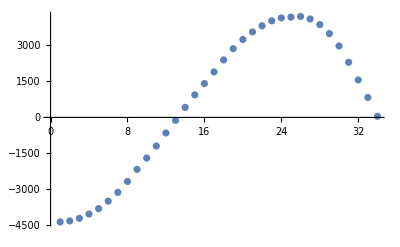

```mathematica
ListPlot[firIn]
```

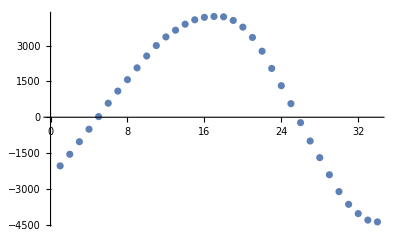

-Graphics-

```mathematica
firOut
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
LongestCommonSubsequence[firOutExp,firOut]
```

{}

```mathematica
s
```

s

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

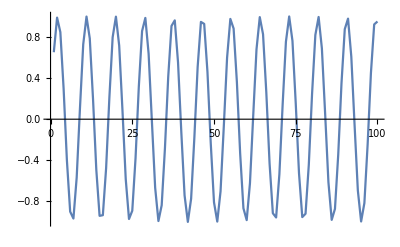

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Append[Flatten@Riffle[in,0],0]
```

{0.651834,0,0.988652,0,0.847678,0,0.297042,0,-0.397148,0,-0.899405,0,-0.967001,0,-0.567269,0,0.106611,0,0.728969,0,0.999033,0,0.786288,0,0.193549,0,-0.492727,0,-0.940881,0,-0.934329,0,-0.476238,0,0.212007,0,0.797794,0,0.998027,0,0.715936,0,0.0878512,0,-0.58269,0,-0.971632,0,-0.891007,0,-0.379779,0,0.314987,0,0.857527,0,0.985645,0,0.637424,0,-0.0188484,0,-0.666012,0,-0.991308,0,-0.837528,0,-0.278991,0,0.414376,0,0.907484,0,0.962028,0,0.551646,0,-0.125333,0,-0.741742,0,-0.999684,0,-0.774503,0,-0.175023,0,0.509041,0,0.947098,0,0.927445,0,0.45958,0,-0.230389,0,-0.809017,0,-0.996666,0,-0.70265,0,-0.06906,0,0.597905,0,0.975917,0,0.882291,0,0.362275,0,-0.33282,0,-0.867071,0,-0.982287,0,-0.622788,0,0.0376902,0,0.679953,0,0.993611,0,0.827081,0,0.260842,0,-0.431456,0,-0.915241,0,-0.956712,0,-0.535827,0,0.144011,0,0.754251,0,0.99998,0,0.762443,0,0.156434,0,-0.525175,0,-0.952979,0,-0.920232,0,-0.442758,0,0.24869,0,0.819952,0,0.994951,0,0.689114,0,0.0502443,0,-0.612907,0,-0.979855,0,-0.873262,0,-0.344643,0,0.350534,0,0.876307,0,0.978581,0,0.60793,0,-0.0565185,0,-0.693653,0,-0.995562,0,-0.816339,0,-0.242599,0,0.448383,0,0.922673,0,0.951057,0}

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0];
```

```mathematica
LinInt[list_]:=Module[{i,intlist={}},For[i=1,i< Length[list],i++,AppendTo[intlist,list[[i]]];AppendTo[intlist,(list[[i]]+list[[i+1]])/2]];AppendTo[intlist,Last[list]];AppendTo[intlist,2*Last[intlist]-intlist[[-2]]];intlist]
```

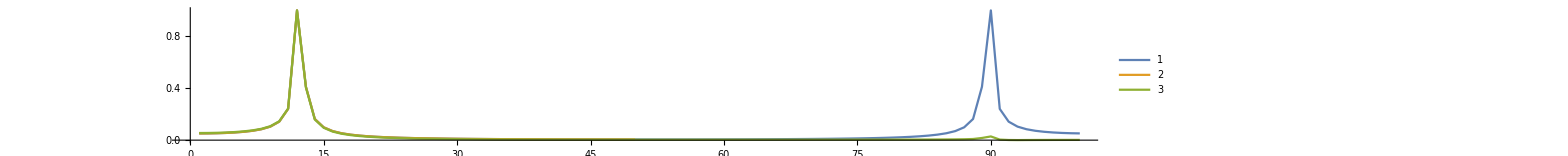

```mathematica
ListPlot[{Half@Abs@Fourier@inR/Max[Half@Abs@Fourier@inR],(Half@Abs@Fourier@in)/Max[Half@Abs@Fourier@in],(Half@Abs@Fourier@LinInt@in)/Max[Half@Abs@Fourier@LinInt@in]},Joined->True,PlotRange->All,ImageSize->5000, PlotLegends->Automatic,AspectRatio->0.1]
```

```mathematica
Manipulate[ListPlot[Abs@Fourier@Flatten@Riffle[Sin[2*π*f*#]&/@Range[100],{{0,0}}],Joined->True,ImageSize->300,PlotRange->{0,3}],{f,0,0.5,0.01}]
```

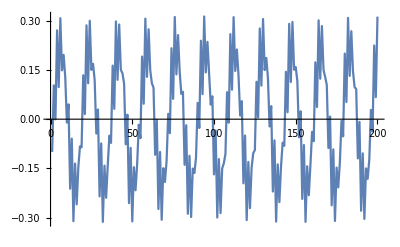

```mathematica
ListPlot[out,Joined->True]
```